```mathematica
b[n_] := 3 * n + 1
```

```mathematica
a[n_] := 2*n + 1
```

```mathematica
collatz[n_] := If[EvenQ[n], n/2, 3n + 1]
```

```mathematica
totient[n_Integer] := Length[ResourceFunction["CoprimeIntegerList"][n]]
triangle[n_Integer] := n(n+1)/2
```

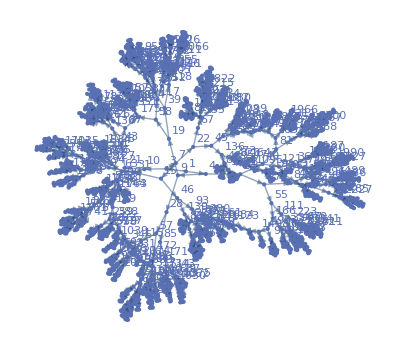

```mathematica
NestGraph[n|->{a[n], b[n]}, 1,10, VertexLabels->Automatic]
```

```mathematica
ResourceFunction["NestGraphTagged"][n↦{a[n], b[n]},{0},7,"StateLabeling"->True,PlotLegends->TraditionalForm/@{a[n],b[n]}]
```

-Graphics-

```mathematica
Graph3D[ResourceFunction["NestGraphTagged"][n↦{n+7,n+11},{0},20],VertexSize->.5,VertexStyle->Darker[RGBColor[0.9215683283650572, 0.9294118431048657, 0.9411764788496759, 1],.25]]
```

-Graphics3D-

```mathematica
With[{g=ResourceFunction["GraphRemoveLooseEnds"][ResourceFunction["NestGraphTagged"][n|->{2 n+1,3 n+1},{0},8,"StateLabeling"->True],All]},Graph[g,EdgeStyle->Catenate[EdgeList@Subgraph[g,PathGraph[First@FindPath[g,#,175],DirectedEdges->True]]/.e:DirectedEdge[_,_,t_]:>e->Directive[{RGBColor[0.91, 0.16379999999999995, 0., 1],RGBColor[0.08499999999999998, 0.39100000000000024, 0.85, 1]}[[t]],Thickness[0.02]]&/@{3,4}]
]
]
```

-Graphics-

```mathematica
SortBy[Graph[#,GraphLayout->"SpringElectricalEmbedding",ImageSize->{Automatic,UpTo[100]}]&/@WeaklyConnectedGraphComponents[EdgeDelete[Graph[With[{g=ResourceFunction["NestGraphTagged"][n↦{3 n,Floor[n/2]},{1},10,"StateLabeling"->True]},Subgraph[g,VertexList[Flatten[FindCycle[UndirectedGraph[g],{4},All]]]]]],{DirectedEdge[5,2,2],DirectedEdge[81,40,2],DirectedEdge[91,45,2],DirectedEdge[29,14,2],DirectedEdge[3,1,2],DirectedEdge[9,4,2]}]],Min[VertexList[#]]&]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
funcs = {a[n], b[n]}
```

{1+2 n,1+3 n}

```mathematica
ResourceFunction["NestGraphTagged"][n↦{totient[n], n - totient[n] },{1138},20,"StateLabeling"->True,PlotLegends->TraditionalForm/@{totient[n], common[n]}]
```

-Graphics-

interesting property with totient and sharing a common factor--eventually all can devolve to a sequence of powers of 2???? conjecture--possible lower bound for hitting a certain power of 2 that seems surprisingly long
https://math.stackexchange.com/questions/2600457/finding-all-n-for-which-phin-is-power-of-2

```mathematica
ResourceFunction["NestGraphTagged"][n↦{a[n], b[n]},{1/Sqrt[2] + ⅈ/Sqrt[2]},3,"StateLabeling"->True,PlotLegends->TraditionalForm/@{a[n], b[n]}]
```

-Graphics-

```mathematica
ResourceFunction["NestGraphTagged"][n↦{3n-13, 4n-1},{1},5,"StateLabeling"->True,PlotLegends->TraditionalForm/@{a[n], b[n]}]
```

-Graphics-

```mathematica
ResourceFunction["NestGraphTagged"][n↦{n^2,Conjugate[n] * ⅇ^(ⅈ*3Pi/7)},{1/Sqrt[2]+ⅈ/Sqrt[2]},10,"StateLabeling"->True,PlotLegends->TraditionalForm/@{n^2,Conjugate[n] * ⅇ^(ⅈ*3Pi/7)}]
```

-Graphics-

```mathematica
ResourceFunction["NestGraphTagged"][n↦{Gamma[n], LaplaceTransform[b[t], t, n]},{6-ⅈ},3,"StateLabeling"->True,PlotLegends->TraditionalForm/@{Gamma[n], LaplaceTransform[b[t], t, n]}]
```

-Graphics-

```mathematica
ResourceFunction["NestGraphTagged"][n↦{Fibonacci[n], 4n-1},{1},4,"StateLabeling"->True,PlotLegends->TraditionalForm/@{a[n], b[n]}]
```

-Graphics-

```mathematica
ResourceFunction["NestGraphTagged"][n↦{2n, n+7},{1},7,"StateLabeling"->True,PlotLegends->TraditionalForm/@{2n, n+6}]
```

-Graphics-

```mathematica
dyckNextCol[lst_List, n_Integer] := Table[Append[lst, i], {i, Range[Last[lst], Length[lst]]}]
```

```mathematica
dyckNextCol[{0, 1, 1,2, 3}, 6]
```

{{0,1,1,2,3,3},{0,1,1,2,3,4},{0,1,1,2,3,5}}

```mathematica
fullDyckList[lst_List, n_Integer] := If[Length[lst] != n, ArrayPad[lst, {0, n - Length[lst]}], Append[lst, n]]
```

```mathematica
fullDyckList[{0, 1, 1, 2, 3}, 6]
```

{0,1,1,2,3,0}

```mathematica
dyckGraphDisplay[lst_List, n_Integer] := Graphics[{Blue, Arrow[
Partition[
Flatten[
Table[
Join[{{i-1, lst[[i]]}, {i , lst[[i]]}},
Flatten[
Table[{{i, j}, {i, j+1}}, {j, Range[lst[[i]], lst[[i + 1]] - 1]}], 1
]
]
, {i, Length[lst]-1}], 1]
,2]
],Red, Dashed, Line[{{0, 0}, {n, n}}]}, Frame->True, GridLines->Automatic]
```

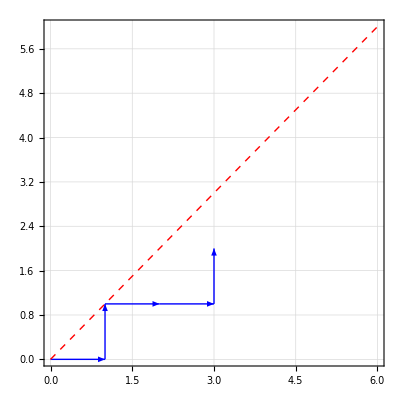

```mathematica
dyckGraphDisplay[{0, 1, 1, 2}, 6]
```

```mathematica
dyckNext[lst_List, n_Integer] := Module[{x := Last[lst][[2]][[1]], y := Last[lst][[2]][[2]]},
Which[
Length[lst] == 0, {{{0, 0}, {1, 0}}},
x==n, {{{x, y}, {x, y+1}}},
x > y, {{{x, y}, {x + 1, y}}, {{x, y}, {x, y + 1}}}, 
True,{{{x, y}, {x + 1, y}}}
]
]
```

```mathematica
dyckNext[{{{0, 0}, {1, 0}}}, 6]
```

{{{1,0},{1,1}},{{1,0},{2,0}}}

```mathematica
generateDyckPath[n_Integer] := Module[{lst = {}},
Last[Table[AppendTo[lst, RandomChoice[dyckNext[lst, n]]], {i, Range[2*n]}]]
]
```

```mathematica
generateDyckPath[3]
```

{{{0,0},{1,0}},{{1,0},{2,0}},{{2,0},{2,1}},{{2,1},{2,2}},{{2,2},{3,2}},{{3,2},{3,3}}}

```mathematica
n=6
dyckGraph[generateDyckPath[n], n]
```

6

-Graphics-

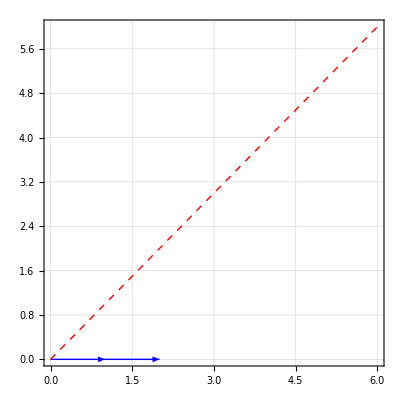
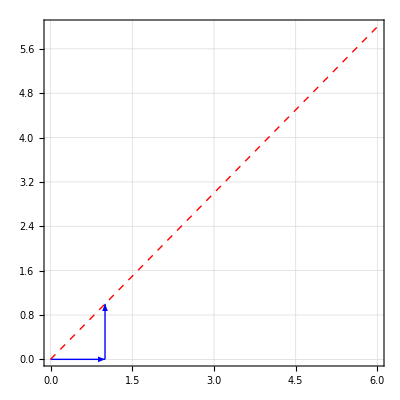

```mathematica
dyckGraph[# , n]& /@(Append[{{{0,0},{1,0}}}, #] & /@ dyckNext[{{{0,0},{1,0}}}, 6])
```

```mathematica
modDyckGraph[#, 3, {0, 2, 2, 3}, {{{1, 0}, {2, 0}}}]& /@ (Append[{{{0,0},{1,0}}}, #] & /@ modDyckNext[{{{0,0},{1,0}}}, 3, {0, 2, 2, 3}, {{{1, 0}, {2, 0}}}])
```

{-Graphics-}

```mathematica
dyckGraph[lst_List, n_Integer] := Graphics[{Blue, Arrow[
Partition[
Flatten[lst, 1]
,2]
],Red, Dashed, Line[{{0, 0}, {n, n}}]}, (*Frame->True,*) GridLines->{Range[0,n, 1], Range[0,n, 1]}, ImageSize->15]
```

```mathematica
dyckGraph[{{{0, 0}, {1, 0}}, {{1,0},{1,1}}}, 6]
```

-Graphics-

```mathematica
modDyckNext[lst_List, n_Integer, resCol_List:Range[0, 10], badEdges_List : {}] := Module[{x, y},
x = If[Length[lst] != 0, Last[lst][[2]][[1]], 0];
y = If[Length[lst] != 0, Last[lst][[2]][[2]], 0];
Which[x==n, {{{x, y}, {x, y + 1}}}, True, Select[{{{x, y}, {x + 1, y}}, {{x, y}, {x, y + 1}}}, #[[2]][[2]]<=resCol[[#[[2]][[1]] + 1]] && !MemberQ[badEdges, #]&]]
]
```

```mathematica
modDyckNext[{{{0,0},{1,0}}}, 3, {0, 2, 2, 3}, {{{1, 0}, {2, 0}}}]
```

```mathematica
{{{1,0},{1,1}}}
```

{{{1,0},{1,1}}}

```mathematica
modDyckNext[{}, 3, {1, 2, 3, 3}]
```

{{{0,0},{1,0}},{{0,0},{0,1}}}

```mathematica
modDyckGraph[lst_List, n_Integer, resCol_List:Range[0, 10], badEdges_List : {}] := Graphics[{Blue, Arrow[
Partition[
Flatten[lst, 1]
,2]
],Red, Dashed, Line[#] & /@ Table[{{i - 1, resCol[[i]]}, {i, resCol[[i + 1]]}}, {i, Range[n]}], Line[#] & /@ badEdges},  GridLines->{Range[0,n, 1], Range[0,n, 1]}, ImageSize->15]
```

```mathematica
modDyckGraph[{{{0,0},{1,0}},{{1,0},{2,0}},{{2,0},{2,1}},{{2,1},{2,2}},{{2,2},{3,2}},{{3,2},{3,3}}}, 3, {0, 2, 2, 3}, {{{1, 0}, {1, 1}}}]
```

-Graphics-

```mathematica
modGenDyckPath[n_Integer, resCol_List:Range[0, 10], badEdges_List : {}] :=  Module[{lst = {}},
Last[Table[AppendTo[lst, RandomChoice[modDyckNext[lst, n, resCol, badEdges]]], {i, Range[2*n]}]]
]
```

```mathematica
modGenDyckPath[3, {0, 2, 2, 3}, {{{1, 0}, {2, 0}}}]
```

{{{0,0},{1,0}},{{1,0},{1,1}},{{1,1},{2,1}},{{2,1},{2,2}},{{2,2},{3,2}},{{3,2},{3,3}}}

```mathematica
ResourceFunction["NestGraphTagged"][lst↦ Append[lst, #] & /@ dyckNext[lst, n],{{}},4,"StateLabeling"->True, PlotLegends -> TraditionalForm /@ {Right, Up}]
```

-Graphics-

```mathematica
ResourceFunction["NestGraphTagged"][lst↦ dyckNext[lst, n],{{}},4,"StateRenderingFunction"->(dyckGraph[#, n] &)]
```

Part::partd: Part specification 0⟦1⟧ is longer than depth of object.

Failure[…]

```mathematica
showGraph[graphs_List, level_Integer]:=ResourceFunction["MultiwaySystem"][<|"StateEvolutionFunction"->Function[list, Append[list, #] & /@ dyckNext[list, n]],"StateEquivalenceFunction"->SameQ,|>,{graphs},level,"StatesGraph","StateRenderingFunction"->(Inset[dyckGraph[#2, n], #1]&)]
```

```mathematica
showGraph[{}, n + 3]
```

-Graphics-

```mathematica
genGraph[] := Function[list, Append[list, #] & /@ dyckNext[list, n]]
(*showGraph[graphs_List, level_Integer] :=ResourceFunction["MultiwaySystem"][<|"StateEvolutionFunction"->genGraph[], "StateEquivalenceFunction"->SameQ|>, {graphs}, level, "StatesGraph", "StateRenderingFunction" ->(Inset[dyckGraph[#2], #1]&)]*)
showGraph[graphs_List, level_Integer]:=ResourceFunction["MultiwaySystem"][<|"StateEvolutionFunction"->genGraph[],"StateEquivalenceFunction"->SameQ,|>,{graphs},level,"StatesGraph","StateRenderingFunction"->(Inset[dyckGraph[#2, n], #1]&)]
```

```mathematica
n=6
```

6

```mathematica
modShowGraph[graphs_List, level_Integer, resCol_List: Range[0, 10], badEdges_List:{}]:=ResourceFunction["MultiwaySystem"][<|"StateEvolutionFunction"->Function[list, Append[list, #] &  /@ modDyckNext[list, n, resCol, badEdges]],"StateEquivalenceFunction"->SameQ,|>,{graphs},level,"StatesGraph","StateRenderingFunction"->(Inset[modDyckGraph[#2, n, resCol, badEdges],#1]&)]
```

```mathematica
modShowGraph[{}, 2*n, {1, 2, 2, 3, 5, 5}]
```

-Graphics-

```mathematica
showGraph[{}, n+3]
```

-Graphics-

```mathematica
Dynamic[n]
n=4
Slider[Dynamic[n], {1, 10, 1}]
Dynamic[ListAnimate[Table[showGraph[{}, moves], {moves, Range[2 * n]}], AnimationRunning->False]]
```

4

```mathematica
Dynamic[Animate[Table[showGraph[{}, n], {i, Range[2 * n]}][[2]], {moves, Range[2 * n]}, {n, 1, 10, 1}, AnimationRunning->False]]
```

```mathematica
ResourceFunction["MultiwaySystem"][
"StateEvolutionFunction"->genGraph[]]
```

```mathematica
ResourceFunction["MultiwaySystem"][lst↦ Append[lst, #] & /@ dyckNext[lst, n],{{}},4,"StateLabeling"->True, "StateRenderingFunction"->(dyckGraph[#1, n]&)]
```

```mathematica
[Function[lst,(Append[lst,#1]&)/@dyckNext[lst,n]],{{}},4,"StateLabeling"->True,"StateRenderingFunction"->(Inset[dyckGraph[#1,n]]&)]
```

```mathematica
[Function[lst,(Append[lst,#1]&)/@dyckNext[lst,n]],{{}},4,"StateLabeling"->True,"StateRenderingFunction"->(Inset[dyckGraph[#1,n]]&)]
```

```mathematica
dyckGraphVis[lst_List, n_Integer, k_Integer] := Graphics[{Blue, Arrow[
Partition[
Flatten[lst, 1],2]
], Purple,Arrow[Select[Partition[
Flatten[lst, 1],2], #[[1]][[2]] >= k
&] ], Green, Arrow[Select[Partition[
Flatten[lst, 1],2], k >=#[[2]][[1]] > 1&&#[[2]][[2]]<k&]],Red, Dashed, Line[{{0, 0}, {n, n}}], Line[{{1, 0}, {k, k - 1}}]}, GridLines->{Range[0,n, 1], Range[0,n, 1]}, ImageSize->Medium]
```

```mathematica
genVisPath[n_Integer, k_Integer] := Module[{lst = modGenDyckPath[k, Range[0, k], Table[{{i, i-1}, {i, i}}, {i, Range[k-1]}]]},
If[n!=k, Last[Table[AppendTo[lst, RandomChoice[dyckNext[lst, n]]], {i, Range[2*(n-k)]}]], lst]
]
```

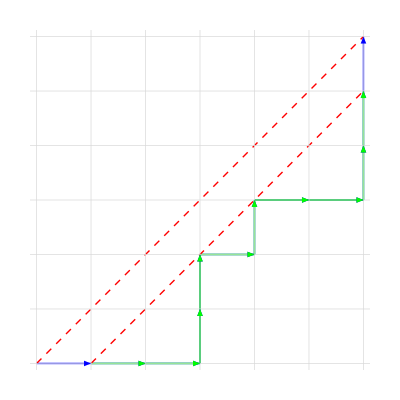

```mathematica
dyckGraphVis[genVisPath[6, 6], 6, 6]
```

```mathematica
Dynamic[ListAnimate[Table[dyckGraphVis[genVisPath[n, k], n, k], {k, Range[n]}], AnimationRunning->False]]
```

```mathematica
path=generateDyckPath[6]
```

{{{0,0},{1,0}},{{1,0},{2,0}},{{2,0},{2,1}},{{2,1},{3,1}},{{3,1},{3,2}},{{3,2},{3,3}},{{3,3},{4,3}},{{4,3},{4,4}},{{4,4},{5,4}},{{5,4},{6,4}},{{6,4},{6,5}},{{6,5},{6,6}}}

```mathematica
Partition[Flatten[path, 1],2]
Select[Partition[Flatten[path, 1],2], #[[2]][[1]] > 6-3&] 
Select[Partition[Flatten[path, 1],2], 3 >#[[2]][[1]] > 1&]
```

{{{0,0},{1,0}},{{1,0},{2,0}},{{2,0},{2,1}},{{2,1},{3,1}},{{3,1},{3,2}},{{3,2},{3,3}},{{3,3},{4,3}},{{4,3},{4,4}},{{4,4},{5,4}},{{5,4},{6,4}},{{6,4},{6,5}},{{6,5},{6,6}}}

{{{3,3},{4,3}},{{4,3},{4,4}},{{4,4},{5,4}},{{5,4},{6,4}},{{6,4},{6,5}},{{6,5},{6,6}}}

{{{1,0},{2,0}},{{2,0},{2,1}}}

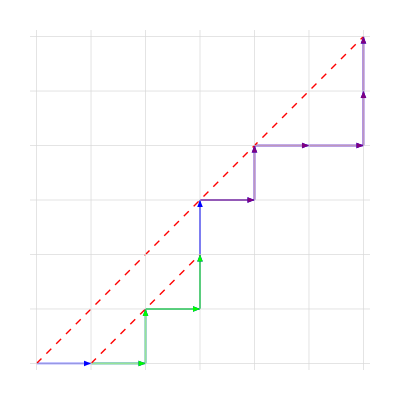

```mathematica
dyckGraphVis[path, 6, 3]
```

```mathematica
|
```

```mathematica
fallingFact[x_Integer, n_Integer] := Product[i, {i,Range[x-n +1, x] }]
```

```mathematica
fallingFact[6, 4]
```

360

```mathematica
risingFact[x_Integer, n_Integer] := Product[i, {i, Range[x, x + n -1]}]
```

```mathematica
risingFact[3, 4]
```

360

```mathematica
ran = 2
ResourceFunction["NestGraphTagged"][n↦{risingFact[n, ran], fallingFact[n, ran]},{3},5,"StateLabeling"->True,PlotLegends->TraditionalForm/@{risingFact[n], fallingFact[n]}]
```

2

-Graphics-

```mathematica
ResourceFunction["NestGraphTagged"][n↦{3*Floor[n] + 2, 2*Ceiling[n] - 5, Round[Log2[2n^2-n+5]]},{1},4,"StateLabeling"->True,PlotLegends->TraditionalForm/@{2n, n+6, 5n-3}]
```

-Graphics-

```mathematica
ResourceFunction["NestGraphTagged"][n↦{(n+1)^2, 2n},{1},16, "PostProcessGraph"->(ResourceFunction["GraphRemoveLooseEnds"][#,All]&)]
```

-Graphics-

```mathematica
ResourceFunction["NestGraphTagged"][n |-> {n^2 - n - 1, n - 1}, 1, 16, "StateLabeling" -> True,PlotLegends->TraditionalForm/@{n^2 - n - 1, n - 1},"PostProcessGraph"->(ResourceFunction["GraphRemoveLooseEnds"][#,All]&)]
```

```mathematica
ResourceFunction["GraphRemoveLooseEnds"][ResourceFunction["NestGraphTagged"][n|->Simplify[{n+1,n (1+Sqrt[2])}],1,12],All]
```

```mathematica
{{"[◼]", "TTTGraph"}}[2,{{{{0,0},{0,0}},1}},2,AspectRatio->.26,
VertexSize->1.1,GraphLayout->"LayeredEmbedding"]
```

-Graphics-

```mathematica
Row[WeaklyConnectedGraphComponents[{{"[◼]", "StyledDeletionsGraph"}}[
{{"[◼]", "MultiwayDeletionsGraph"}}[GridGraph[{2,2}]],
GridGraph[{2,2}],ImageSize->150,VertexSize->1]],Spacer[30]]
```

```mathematica
With[{gKonigsbergFixed=Graph[{
UndirectedEdge[n1,n2],UndirectedEdge[s1,s2],
UndirectedEdge[n1,w],UndirectedEdge[n2,w],
UndirectedEdge[s1,w],UndirectedEdge[s2,w],
UndirectedEdge[e,w],UndirectedEdge[n1,e],
UndirectedEdge[s1,e]},
EdgeStyle->Directive[Thick,GrayLevel[.4]],VertexSize->.2,
VertexStyle->Directive[EdgeForm[GrayLevel[.4]],GrayLevel[.7]]]},
{{"[◼]", "StyledEdgeDeletionsGraph"}}[{{"[◼]", "MultiwayDeletionsGraph"}}[gKonigsbergFixed,{e},
EdgeDelete,GraphLayout->"LayeredDigraphEmbedding"],
Graph[gKonigsbergFixed,VertexSize->.4`],VertexSize->1.35,ImageSize->640]]
```

stealing henry’s code

```mathematica
ClassicStartingBoard={{0,0,0},{0,0,0},{0,0,0}};
```

```mathematica
BoardImage[{{1,0,0},{2,0,0},{0,1,0}}]
FlipVertical[list_]:=Reverse[list]
BoardImage[FlipVertical[{{1,0,0},{2,0,0},{0,1,0}}]]
FlipHorizontal[list_]:=Reverse/@list
BoardImage[FlipHorizontal[{{1,0,0},{2,0,0},{0,1,0}}]]
FlipDiagonal[list_]:=Transpose[list]
BoardImage[FlipDiagonal[{{1,0,0},{2,0,0},{0,1,0}}]]
```

-Graphics-

-Graphics-

-Graphics-

«1 more identical outputs»

```mathematica
FindSymmetricalCopies[bigList_,element_]:=Position[((element===FlipVertical[#]||element===FlipHorizontal[#]||element===FlipDiagonal[#]||element===FlipDiagonal[Reverse[#]])&&Position[bigList,#][[1]][[1]]>Position[bigList,element][[1]][[1]])&/@bigList,True]
```

```mathematica
RemoveSymmetries[list_]:=Delete[list,List/@(Flatten[(FindSymmetricalCopies[list,#])&/@list])]
```

```mathematica
GeneratingBoardsFunction[list_]:=RemoveSymmetries[ReplacePart[list,#->If[Count[Flatten@list,1]==Count[Flatten[list],2],1,2]]&/@Position[list,0]]
BoardImage[list_]:=ArrayPlot[list,ColorRules->{0->White,1->Red,2->Blue},ImageSize->20,Mesh->True]
```

```mathematica
GenerateBoards[]:=Function[list,GeneratingBoardsFunction[list]]
ShowGraph[moves_Integer,board_List]:=ResourceFunction["MultiwaySystem"][<|"StateEvolutionFunction"->GenerateBoards[],"StateEquivalenceFunction"->SameQ,|>,{board},moves,"StatesGraph","StateRenderingFunction"->(Inset[BoardImage[#2],#1]&)]
```

```mathematica
ShowGraph[3, ClassicStartingBoard]
```

-Graphics-